```mathematica
SetDirectory@NotebookDirectory[]
```

/home/eduard/lectures/koheraente_optik/praktikum

## Fitting a gaussian beam

```mathematica
gaussian[x_,a_,b_,x0_]:=a ⅇ^(-b (x-x0)^2)
erfc[x_,a_,w_,x0_]:=a Erfc[(x-x0)/(2w)]
fitGaussian[data_]:=FindFit[data,gaussian[x,a,b,x0],{a,b,x0},x]
fitErfc[data_]:=FindFit[data,erfc[x,a,w,x0],{a,w,x0},x]
```

```mathematica
fitErfc[sample[[All,2;;3]]]
fwhmAtZ[sample_]:=({sample[[1,1]],w}
/.fitErfc[sample[[All,2;;3]]]
(*fwhm->2 √(Log[2]/b)]*))
divAngleAndWaistLocation[sample_]:={Θ-> ArcTan[a]z0-> -b/a}/.FindFit[
fwhmAtZ/@GatherBy[sample,First]
,a x + b, {a,b},x]

plotFitAtZ[sample_]:=
{sample[[1,1]],
w/.fitErfc[sample[[All,2;;3]]],
Show[{
ListPlot[sample[[All,2;;3]],PlotTheme->"Scientific"],Plot[Evaluate[erfc[x,a,w,x0]/.fitErfc[sample[[All,2;;3]]],{x,-5,5},PlotRange->Full],
PlotTheme->"Scientific"]
}]
}
```

{a→1.44054,w→3.387,x0→0.711043}

{1,3.8722}

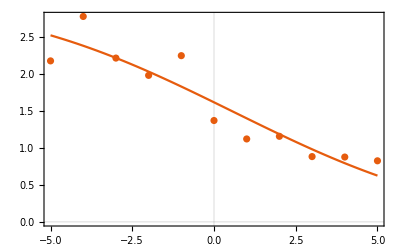
{1,3.8722,-Graphics-}

```mathematica
(* test for one z location *)
sample ={ 1,#, erfc[#,1,2,0]+RandomReal[1]}&/@Range[-5,5,1];
fwhmAtZ[sample]
plotFitAtZ[sample]
```

bla.csv

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{Θ→1.37209 z0→2.05111}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

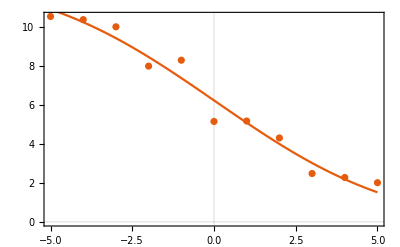
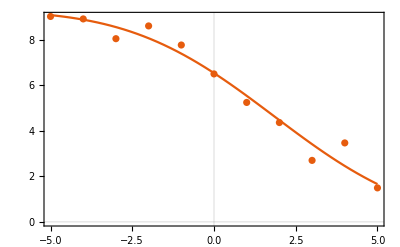
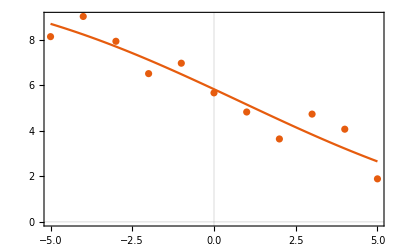
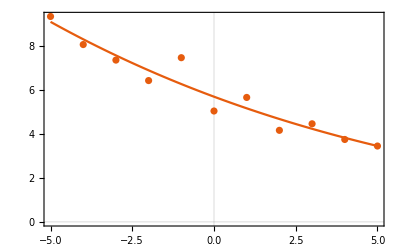
{{2,3.0198,-Graphics-},{3,2.43293,-Graphics-},{4,4.41636,-Graphics-},{5,18.9125,-Graphics-}}

```mathematica
sample =Tuples[{Range[2,5,1],Range[-5,5,1]}]/.{z_,y_}:>{z ,y, erfc[y,5,z,0]+RandomReal[2]};
Export["bla.csv", sample]

(*dataps=ListPlot/@GatherBy[sample,First][[All,All,2;;3]]*)(*
div=fwhmAtZ/@GatherBy[sample,First]*)

divAngleAndWaistLocation[sample]
plotFitAtZ/@GatherBy[sample,First]
```